```mathematica
Lecture 1:Conceptual Introductions
```

# Science and Data Science

## Science

Oxford dictionary: Systematic study of the structure and behaviour of the physical and natural world through observation and experiment

## Data Science

It is a multidisciplinary evolving and dynamic field, with several incipient definitions.

[Wikipedia] Interdisciplinary field about processes and systems to extract knowledge or insights from data in various forms, either structured or unstructured.

[Hayashi, Chikio, 1998]  Data science is a “concept to unify statistics, data analysis and their related methods” in order to “understand and analyze actual phenomena” with data.

[Chirag Shah] A field of study and practice that involves the collection, storage, and processing of data in order to derive important insights into a problem or a phenomenon.

Turing award winner Jim Gray imagined data science as a “fourth paradigm” of science (empirical, theoretical, computational and now data-driven) and asserted that “everything about science is changing because of the impact of information technology” and the data deluge.

[M. S. Baptista] It is the scientific method applied to data (any type of data), and supported by approaches and tools from different disciplines.

“The sexist job of the 21st century”

```mathematica
Let’s talk about data!
```

Link

175 ZB by end of 2025 is more than 85-fold that of 2010.

Byte (B): The basic unit, 8 bits.
Kilobyte (KB): ~1,000 bytes (1024 in computing).
Megabyte (MB): ~1,000 KB (1024 KB).
Gigabyte (GB): ~1,000 MB (1024 MB).
Terabyte (TB): ~1,000 GB (1024 GB).
Petabyte (PB): ~1,000 TB (1024 TB).
Exabyte (EB): ~1,000 PB (1024 PB).
Zettabyte (ZB): ~1,000 EB (1024 EB).
Yottabyte (YB): ~1,000 ZB (1024 ZB).

1 ZB (Zettabyte) = 1000^7bytes = 10^21bytes = 1000000000000000000000bytes = 1000exabytes = 1millionpetabytes = 1billionterabytes = 1trilliongigabytes.

# 3 V model of data

Velocity: The speed in which data is accumulated increased

Volume: The size and scope of the data increased

Variety: The massive array of data and types (structured and unstructured) increased

# Data Science applications in different domains

Finance: minimizing loan default by mining customer profile, past expenditure, analyse customer purchase power to seel products, fraud detection.

a project: construct a predicting model for loan eligibility from Lending Club loan dataset, Notes1 .7-updated, Notes1.8. (these are notes from TB Shah), by identifying from historical loan data the applicants that are relatively risky for loan.

Recession in real time: how big data can track the Covid slump in 2020 [the Guardian].

-Graphics-

X (formally Twitter) sentiment data can be used as a predictor for firm’s share prices [Juma'h 2018].

Analyzing product usage and customer behavior to drive recommendations for improved customer experience across business units (customer data).

Mastercard’s “Decision Intelligence” platform. This system utilizes advanced data science techniques to analyze billions of transactions in real-time to distinguish between legitimate purchases and fraudulent activity.

Public policy:

The New Zealand Social Investment Agency (now the Social Wellbeing Agency) uses an integrated data infrastructure to identify children at the highest risk of long-term disadvantage, Link.

At TOSSIB and SASSI we worked to understand how UN SDG are linked together to understand how investment in one of them can improve other goals. Students from the 2021/2022 cohorts have done their thesis in this topic. Very interesting to see how the network analysis of the interlinkage structure of SDGs provides information about the social economic state of a nation (unsupervised learning).

Tossib has supported 3 RAs (master students from 2022/2023 cohort) to understand how sanitation structure links to well being

7 summer projects (cohort 2022/2023) were based on the study of the The China Health and Retirement Longitudinal Study (CHARLS) survey dataset.

Several open data initiatives to allow data scientists to gain insights into citizen behaviours that affect the quality of public life (traffic, transportation, social welfare, community wellbeing): US government, European Union, the UK.

Politics: Recently, real-time application of data science to politics has skyrocketed.

US Presidential Obama’s 2008 presidential campaign, 2016 campaign to elect  D. Trump to tailor individual messages to individual people, target political ads by using Facebook data (without consent), meddling of Brexit by Russia. Read article Link? The 2024 Trump campaign used behavioral data and psychographics to deliver hyper-specific ads; a “suburban mom” might receive content focused on school safety, while a “rural farmer” saw messages about agricultural deregulation. Link.

Analysis of social media can help predicting voting shares, information that can be used for target ads. Facebook spending ad data [Levy 2020] and Google trends [Prado-Román 2020] .

Economics: BREXIT: there is much data analysis about the impact of BREXIT in the UK economy [Wikipedia]. Data has shown that “Brexit exodus helps drive record number in EU banks paid €1m-plus” [The Guardian, Jan. 2023]

Healthcare:

data scientists can help understand what treatment works and for whom from health records data. Tutorial 9 will deal with this.

Predictive analytics are strengthening disease detection and patient monitoring for earlier interventions and personalized care. (N. Rubido and I are working with detection of Dementia from EEG.)

predicting hospital patient admission, and length of stay (Mamen Romano).

In the course, we will also deal with a series of other applications of data science.

# Relation of Data Science with other fields

Notice that this is also connected to the information from previous slides on applications

Statistics:

Statistics provides a powerful way to prepare, explore and construct statistical models of data, and to allow us to understand it. Data science allows statistical tools and approaches to be used to large and  heterogeneous datasets. But it offers also other techniques and approaches of analysis.

Computer Science:

Database systems

Visualization techniques

Computer languages (not only created by computer scientists)

Algorithms

Several machine learning techniques

Artificial intelligence

Decision processes

Engineering:

has given to Data Science (DS) the central processing unit (CPU), Graphic processing unit (GPU), Controlling techniques used for optimization processes.

DS is relevant for cyber-physical systems, smart systems, such as the smart grid.

DS already is used to design applications (e.g. antennas), to accurately predict project costs.

Physics and applied mathematics :

Information theory

Complex Systems and Networks

causality

time-series and signal analysis

analytical modelling (other than machine learning)

modelling (machine learning) of complex systems.

Mathematics :

Neuron networks chaos-enhanced can model EEG signals [Link]

A 1-layer neural network capable of performing quick and accurate numerical integration by Constantinos Siettos Link.

Several EPSRC funded projects on the Mathematics of Machine Learning.

```mathematica
What skills do we need for Data Science?
```

Willing to experiment: Data scientist needs to have the drive, intuition, and curiosity not only to solve problems as they are presented, but also to identify and articulate problems of their own.

employers are seeking applicants who can answer questions to define intelligent hypothesis and to explore the data utilizing basic statistical methods and models: “How many golf balls would fit in a school bus?”, “How many candies fit in a jar glass”? To solve this you need to :

do an experiment: estimate the volume of candies you can see, and the volume of the glass

do an intelligent hypothesis: the volume of all candies are similar

estimate the total number of candies

Proficiency in mathematical reasoning: you need a strong grasp on the basics statistical methods and how to employ them

employers are seeking applicants who can demonstrate their ability in reasoning, logic, interpreting data, and develop strategies to perform analysis.

Data literacy: the ability to extract meaningful information from a dataset, and to understand what this information convey: If I tell you that there is 10% of chances for raining today, what does this mean?

Computational thinking: coming next

Creative, Team Player, Good communicator, Collegiate spirit.

Scientist thinking: remaining slides....

# Computational thinking

[WikiMedia: A. Repening, A. Basawapatna, and N. Scherle, “Computational Thinking Tools”]

The solution expression can be done by decomposition, were a complex problem is broken down into a set of smaller problems, easier to be solved. “If volume in front of a small piece of mud is empty, move. A physicist would include some more information. Move it if the gravity force is stronger than the friction along the sliding direction.”

Hands-on problem 1.1 [textbook] "what is the largest number of the set: 7, 4, 62, 11, 4, 39, 42, 5, 97, 54?"

Take the largest between 7 and 4

Compare with the next number, keep the largest

Repeat until the end

Do it yourself: how to determine the n-th largest number, ranking?.... (see bellow)

Use the previous algorithm, once  maximal is determined move it to a separate file.  The remaining list of numbers have a new maxima value, which can be determined, and taken to the other list. All numbers will be ranked.

## The structure of a data science project: the data science pipeline

## Why a pipeline?

For reproducibility. By publishing your work, others can run similar analyses to:

verify results (replication == stronger evidence)

build on existing results

combine results for better insight

but also to adapt/redo any substeps of the pipeline whenever necessary

For agile data science

Iterative process of tweaking and improving

Rapid prototyping

The pictured pipeline is the sketch of a project (watch YouTube video).  The picture is oversimplified, giving an almost direct path connecting data to reporting. Order of different tasks may need to be different. The order with which tasks are done is also not necessarily the one that is ideal for your problem.

## Reproducible Research Checklist

Plan out a modular pipeline for the analysis: Data wrangling, Data cleaning, Exploratory analysis, Data preprocessing, ..., as previously described. But further:

Automate wherever possible (e.g. scripts instead of point-and-click)

Document your code

Use version control

Record and preserve:

Sources: raw data, goals, references

Process: explorations, final code, observations and comments (selections and rejections)

Output: clean data, graphics, reports

Prepare for obsolescence (things will change; data sources will get removed)

Prepare for portability

# The Scientific Method

```mathematica
{,}
```

Science [Oxford dictionary] : systematic study of the structure and behaviour of the physical and natural world through observation and experiment.

Thinking as a scientist : understanding the scientific method can help you much to design your data science project.

Recognize a problem, by doing observations:  Where is the Earth in the Universe (in the centre or revolving around the Sun)?

Make a hypothesis:

Ptolemy: the Earth is in the centre, because there is no stellar parallax.

Copernicus: the Earth revolves around the Sun, because Ptolemy model is inaccurate (position and intensity), it is mathematically easier (retrograde motion does not require Epicycles to be explained).

Predict the consequences of hypothesis:

Ptolomy model: Venus cannot have a Full phase

Copernicus model: Venus can have a Full phase, Stellar parallax must exist.

Perform experiments to test predictions: Galileo observed a Full phase of the planet Venus (1610). Stellar parallax first measured in 1838 by Friedrich Bessel.

Find a rule that leads to a theory: Kepler Law’s of motion, followed by Newton Theory of Gravity

Tested hypothesis may become a theory or law

Publish or disseminate your work

Reality is described by a model

# The Scientific Method, and the Data Science

Recognize a problem, by doing observations:  “Question” about a problem, go find the data to answer your question, clean it.

Make a hypothesis: by exploring and pre-processing the data to find underlying properties/patterns, such as a validation set.

Predict the consequences of hypothesis:

Before start any serious work or model (in this course by a regression or machine learning), reflect if hypothesis constructed is plausible

Predictions can be assisted by a model

Perform experiments to test predictions: Validate the model and its predictions using the validation data, or other dataset.

Find a rule that leads to a theory: That would mean that your model can be applied to a large class of data, or systems.

Publish or disseminate your work: Tell your History.

Reality is described by a model: Actionable insight!

## Reality is described by a model: Actionable insight!

After Copernicus, Kepler and Galileo, it became accepted that the Earth was revolving around the Sun. The whole European society needed to be reeducated to accept this now demonstrated natural phenomenon, including the Roman Catholic Church. This was at the time a tremendous government and religion actionable insight!

Related to Covid, there are innumerous examples of how data science provokes actionable insights, not always they are for the benefit of the society.

THE BAD actionable insight:

A paper in The Lancet was retracted [The Guardian]. It was about the effect of Covid patients receiving hydroxychloroquine leading to heartbeat irregularities, and that halted drug tests across the world. The data used had an unreliable source, of a company that has emerged out of nowhere and was claiming to have clinical data from several hospital around the word [The Guardian]. The company has still not explained the source of the data. [read Blog by Derek owe].

THE GOOD actionable insight:

"How Professor Neil Ferguson helped save tens of thousands of lives worldwide — and carried COVID-19 into Downing Street" [Business Insider]. Ferguson’s team warned Boris Johnson that the quest for “herd immunity” could cost 510,000 lives, prompting an abrupt U-turn. His simulations have been influential in other countries as well, cited by authorities in the US, Germany, and France.

# Hands - on example 1.2: Analyzing Data

[TB, by Shah Chapter 1, example 1.2]

Analyzing a dataset about Height and Weight for American Woman

A preliminary glimpse of what kinds of things people do as a data scientist : identify data source, collect the data, clean the data, analyse the data, present our findings.

## Obtaining the data

Typing manually for data, from the table in book, or...

```mathematica
dataset1={{"Observation","Height (inches)","Weight (lbs)"},{1,58,115},{2,59,117},{3,60,120},{4,61,123},{5,62,126},{6,63,129},{7,64,132},{8,65,135},{9,66,139},{10,67,142},{11,68,146},{12,69,150},{13,70,154},{14,71,159},{15,72,164}}//Dataset
```

or importing [Online Appendix 1.1]:

```mathematica
dataset=Import["https://raw.githubusercontent.com/vincentarelbundock/Rdatasets/master/csv/datasets/women.csv"]
```

{{rownames,height,weight},{1,58,115},{2,59,117},{3,60,120},{4,61,123},{5,62,126},{6,63,129},{7,64,132},{8,65,135},{9,66,139},{10,67,142},{11,68,146},{12,69,150},{13,70,154},{14,71,159},{15,72,164}}

Notice that the attribute name "Observation" is not present and the cell instead contains “rownames” (until January 2023 it was empty!)

# Hands - on exercise

Analyzing a dataset about Height ad Weight for American Woman

## Preparing the data:

meaning extraction of the two columns of data for further analysis.

```mathematica
dataset[[1,1]]="Observation"
```

Observation

or, use Replace:

```mathematica
dataset=Import["https://raw.githubusercontent.com/vincentarelbundock/Rdatasets/master/csv/datasets/women.csv"]
```

{{rownames,height,weight},{1,58,115},{2,59,117},{3,60,120},{4,61,123},{5,62,126},{6,63,129},{7,64,132},{8,65,135},{9,66,139},{10,67,142},{11,68,146},{12,69,150},{13,70,154},{14,71,159},{15,72,164}}

```mathematica
dataset=Replace[dataset,"rownames"-> "Observation",{2}]
```

{{Observation,height,weight},{1,58,115},{2,59,117},{3,60,120},{4,61,123},{5,62,126},{6,63,129},{7,64,132},{8,65,135},{9,66,139},{10,67,142},{11,68,146},{12,69,150},{13,70,154},{14,71,159},{15,72,164}}

```mathematica
dataset
```

{{Observation,height,weight},{1,58,115},{2,59,117},{3,60,120},{4,61,123},{5,62,126},{6,63,129},{7,64,132},{8,65,135},{9,66,139},{10,67,142},{11,68,146},{12,69,150},{13,70,154},{14,71,159},{15,72,164}}

Suppose that variables height and weight are obtained from different sources . How can we combine then in a single dataset?

```mathematica
dataset[[2;;,2]]
```

{58,59,60,61,62,63,64,65,66,67,68,69,70,71,72}

```mathematica
height=dataset[[2;;,2]]
```

{58,59,60,61,62,63,64,65,66,67,68,69,70,71,72}

```mathematica
weight=dataset[[2;;,3]]
```

{115,117,120,123,126,129,132,135,139,142,146,150,154,159,164}

```mathematica
{height,weight}//MatrixForm
```

(58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72
115 | 117 | 120 | 123 | 126 | 129 | 132 | 135 | 139 | 142 | 146 | 150 | 154 | 159 | 164)

```mathematica
{height,weight}
```

{{58,59,60,61,62,63,64,65,66,67,68,69,70,71,72},{115,117,120,123,126,129,132,135,139,142,146,150,154,159,164}}

```mathematica
points=Transpose[{height,weight}]
```

{{58,115},{59,117},{60,120},{61,123},{62,126},{63,129},{64,132},{65,135},{66,139},{67,142},{68,146},{69,150},{70,154},{71,159},{72,164}}

We could have done that by simply

```mathematica
points=dataset[[2;;,2;;3]]
```

{{58,115},{59,117},{60,120},{61,123},{62,126},{63,129},{64,132},{65,135},{66,139},{67,142},{68,146},{69,150},{70,154},{71,159},{72,164}}

Discuss different formats of preparing the data you want, points supposedly coming from 2 different sources and need to be integrated, second example, doing a data reduction from a larger dataset.

# Extra slide, a short depart from the hands-on exercise

Data can be put in a Table and the Table can be updated [Mathematica 12.1].

```mathematica
playaroundPoints=points;
```

```mathematica
TableView[Dynamic[playaroundPoints]]
```

$CellContext`playaroundPoints

Let us add some numbers in the table and see what happens:

```mathematica
playaroundPoints
```

{{58,115},{59,117},{60,120},{61,123},{62,126},{63,129},{64,132},{65,135},{66,139},{67,142},{68,146},{69,150},{70,154},{71,0},{72,0}}

The dataset playaroundPoints has been updated.

# Hands - on exercise

Analyzing a dataset about Height and Weight for American Woman

## Exploring the data and modelling

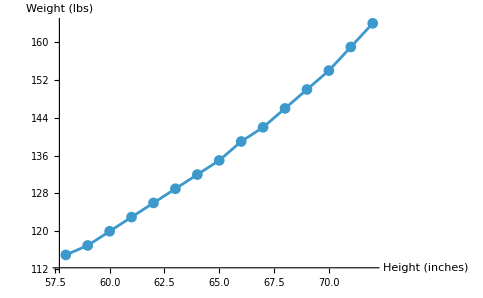

```mathematica
ListLinePlot[points,AxesLabel->{"Height (inches)","Weight (lbs)"},PlotMarkers->Automatic]
```

Let us start calculating averages:

Average for Height:

```mathematica
Total[height]/15
```

65

Average for Weight

```mathematica
Total[weight]/15
```

2051/15

```mathematica
N[%]
```

136.733

explain linear approximations of non-linear functions

discuss meaning of calculated averages.

## New in Mathematica 12.2

To reduce an array or aggregate it to calculate Mean, Total, StandardDeviation along specific dimensions of an array:

1 indicates reduction is done on the rows - each column produces an average.

2 reduction is done on the columns - each row produces an average, for example when each column has information about a variable in different dates/times and one wants a year average.

So, let us "reduce" the rows, calculating the mean values for height and weight

```mathematica
ArrayReduce[Mean,points,1]
```

{65,2051/15}

This is equivalent to

```mathematica
Mean[points]
```

{65,2051/15}

The dataset reveals that an increase in high correlates with an increase in weight

## Modelling the data

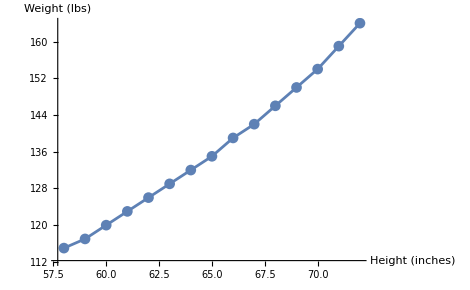

```mathematica
ListLinePlot[points,AxesLabel->{"Height (inches)","Weight (lbs)"},PlotMarkers->Automatic]
```

On average, how much increase can we expect in weight (list weight) with an increase of one inch in height (list height)?

```mathematica
N[(Max[weight]-Min[weight])/(Max[height]-Min[height])]
```

3.5

But this analysis will change depending on the range of values for height we are considering, since the higher the height the higher the weight

For higher height (use 2 last points of data):

```mathematica
(dataset[[16,3]]-dataset[[15,3]])/(dataset[[16,2]]-dataset[[15,2]])
```

5

For lower height (use 2 first points):

```mathematica
(dataset[[3,3]]-dataset[[2,3]])/(dataset[[3,2]]-dataset[[2,2]])
```

2

# Hands - on exercise

Analysing a dataset about Height ad Weight for American Woman

## Predicting the data from the model

What would be the expected weight of an American woman with a height of 57?

We need to extrapolate, using our estimation for the rate of change for lower height : for every 1 inch, there is a change of 2 lbs, so we would estimate a weight of 115-2=113lbs

Do the same for an American woman with a height of 73?Answer = 164+5=169!

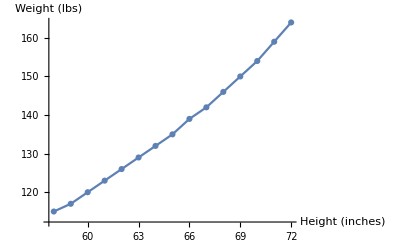

```mathematica
ListLinePlot[points,AxesLabel->{"Height (inches)","Weight (lbs)"},PlotMarkers->Automatic]
```

```mathematica
points
```

{{58,115},{59,117},{60,120},{61,123},{62,126},{63,129},{64,132},{65,135},{66,139},{67,142},{68,146},{69,150},{70,154},{71,159},{72,164}}